# Three Body Decay Event Generator

ThreeBody function takes mass of parent particle M, and mass of three daughter particles m1, m2, m3 as input. The output is a list of three 4-momentum vectors corresponding to the three daughter particles for the randomly chosen decay event.

```mathematica
ThreeBody[M_,m1_,m2_,m3_]:=Module[{m12,m23,m13,E2s,E3s,m23max,m23min,E1,E2,E3,θ,p1,p2,p3,Cosθ,Sinθ},
(*initialize m12 and m23*)
m12=2M;
m23=2M;
E2s = (m12^2-m1^2+m2^2)/(2m12);
E3s = (M^2-m12^2-m3^3)/(2m12);
m23max = (E2s+E3s)^2-(√(E2s^2-m2^2)-√(E3s^2-m3^2))^2;
m23min = (E2s+E3s)^2-(√(E2s^2-m2^2)+√(E3s^2-m3^2))^2;

(*Choose random m12 and m23, until you get kinematically allowed values*)
While[!(m23^2<m23max &&m23^2>m23min&&Abs[(E1 E2-(1/2)(m12^2-m1^2-m2^2))/(√(E1^2-m1^2)√(E2^2-m2^2))]<1),
m12=√RandomReal[{(m1+m2)^2,(M-m3)^2}];
m23=√RandomReal[{(m2+m3)^2,(M-m1)^2}];
E2s = (m12^2-m1^2+m2^2)/(2m12);
E3s = (M^2-m12^2-m3^3)/(2m12);
If[E2s>m2&&E3s>m3,
m23max = (E2s+E3s)^2-(√(E2s^2-m2^2)-√(E3s^2-m3^2))^2;
m23min = (E2s+E3s)^2-(√(E2s^2-m2^2)+√(E3s^2-m3^2))^2;,
m23max=0;
m23max=0;];
E1=(m23^2-M^2-m1^2)/(-2M);
E3=(m12^2-M^2-m3^2)/(-2M);
E2=M-E1-E3;];

(*Solve for 4-momentum. Choose coordinate system so that the decay in M rest frame takes place in x-y plane. Rotate x-y plane so that p1 is along x-axis*)
E1=(m23^2-M^2-m1^2)/(-2M);
E3=(m12^2-M^2-m3^2)/(-2M);
E2=M-E1-E3;
Cosθ=(E1 E2-(1/2)(m12^2-m1^2-m2^2))/(√(E1^2-m1^2)√(E2^2-m2^2));
Sinθ=√(1-Cosθ^2);
p1={E1,√(E1^2-m1^2),0,0};
p2={E2,√(E2^2-m2^2)Cosθ,√(E2^2-m2^2)Sinθ,0};
p3={E3,-√(E1^2-m1^2)-√(E2^2-m2^2)Cosθ,-√(E2^2-m2^2)Sinθ,0};
{p1,p2,p3}]
```

# Examples

Display the 3-momenta of the three daughter particles for a single event. Here the parent has unit mass, and the three daughter particles are massless.

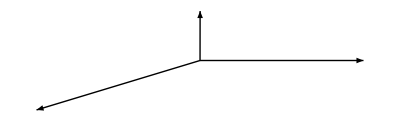

```mathematica
ThreeMomentaList = ThreeBody[1,0,0,0][[All,2;;3]];
Graphics[Table[Arrow[{{0,0},ThreeMomentaList[[i]]}],{i,1,3}]]
```

The histogram displays the energy distribution of the daughter particles. Generated with 10,000 events.

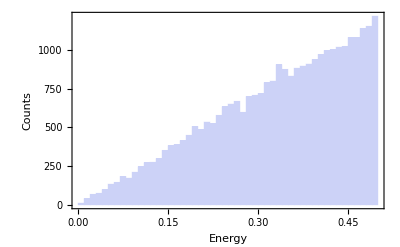

```mathematica
Histogram[
Flatten[
Table[
ThreeBody[1,0,0,0][[All,1]],
{10000}]
],
Frame->True,
FrameLabel->{"Energy","Counts"},
BaseStyle->{FontSize->20}]
```